```mathematica
P1=Import["P1.txt","Table"];
P2=Import["P2.txt","Table"];
Pe=Import["Pe.txt","List"];
(*Pe runs only upto nn=48*)
```

```mathematica
Clear[V];
μ=50;
nn=10;
wc=μ/(nn+1);
{me,ϵ,V}={1,0.1,1};
data={};
For[V=0.01,V≤π,V+=0.05,
{
l=1/Sqrt[me*wc];
En[n_]:=(n+1/2)*wc+(l^4)*(ϵ/4)*Pe[[n+1]];
kf[n_]:=Re[Sqrt[2*(μ-En[n])]];
selfenergy[n_]:=(-1/π)*(1/l)*Sum[P1[[n+1,m+1]]*kf[m],{m,0,nn+1}];
smatrix=Table[(selfenergy[n]-selfenergy[n+1])*KroneckerDelta[n,m],{n,0,nn},{m,0,nn}];
vmatrix=Table[(1/l)*P2[[n+1,m+1]],{n,0,nn},{m,0,nn}];
kmatrix=Table[(1/π)*(kf[n]-kf[n+1])*KroneckerDelta[n,m],{n,0,nn},{m,0,nn}];
M=-kmatrix.vmatrix-smatrix;
MM=Eigenvalues[M];
For[i=0,i≤nn,i++,
{mm=MM[[i+1]];
ω=wc+(l^4)*(ϵ/4)*(Pe[[i+2]]-Pe[[i+1]])+V*mm;
AppendTo[data,{V*me/π,ω/wc}]}];
}]
```

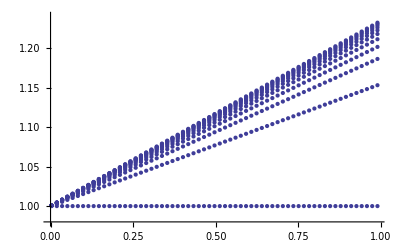

```mathematica
f1=ListPlot[data,PlotRange->{0.98,1.24}]
```

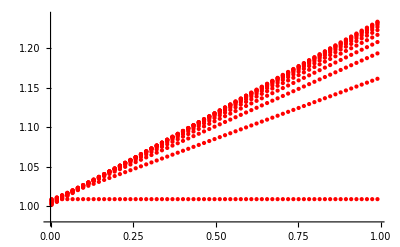

```mathematica
f2=ListPlot[data,PlotStyle->Red,PlotRange->{0.98,1.24}]
```

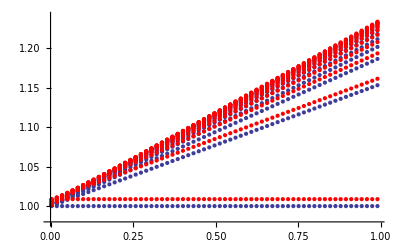

```mathematica
Show[f1,f2]
```